```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Compute an outer product:

```mathematica
AssociationOuter[f,{a,b},{x,y,z}]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

Compare to Outer:

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

Outer product of vectors:

```mathematica
AssociationOuter[Times,{1,2,3,4},{a,b,c}]
```

<|1→<|a→a,b→b,c→c|>,2→<|a→2 a,b→2 b,c→2 c|>,3→<|a→3 a,b→3 b,c→3 c|>,4→<|a→4 a,b→4 b,c→4 c|>|>

Outer product of matrices:

```mathematica
AssociationOuter[Times,{{1,2},{3,4}},{{a,b},{c,d}}]
```

<|1→<|a→a,b→b,c→c,d→d|>,2→<|a→2 a,b→2 b,c→2 c,d→2 d|>,3→<|a→3 a,b→3 b,c→3 c,d→3 d|>,4→<|a→4 a,b→4 b,c→4 c,d→4 d|>|>

### Scope

They keys are nested so that values can be retrieved in argument order:

```mathematica
as=AssociationOuter[f,{a,b},{x,y,z},{u,v}]
```

<|a→<|x→<|u→f[a,x,u],v→f[a,x,v]|>,y→<|u→f[a,y,u],v→f[a,y,v]|>,z→<|u→f[a,z,u],v→f[a,z,v]|>|>,b→<|x→<|u→f[b,x,u],v→f[b,x,v]|>,y→<|u→f[b,y,u],v→f[b,y,v]|>,z→<|u→f[b,z,u],v→f[b,z,v]|>|>|>

```mathematica
as[a,y,u]
```

f[a,y,u]

```mathematica
as[b,x,v]
```

f[b,x,v]

Treat nested lists as rank-1 vectors of sublists:

```mathematica
AssociationOuter[f,{{1,2},{3,4}},{{a,b},{c,d}},1]
```

<|{1,2}→<|{a,b}→f[{1,2},{a,b}],{c,d}→f[{1,2},{c,d}]|>,{3,4}→<|{a,b}→f[{3,4},{a,b}],{c,d}→f[{3,4},{c,d}]|>|>

Arrays can be ragged:

```mathematica
AssociationOuter[Times,{{1,2},{3,4}},{{a,b,c},{d,e}}]
```

<|1→<|a→a,b→b,c→c,d→d,e→e|>,2→<|a→2 a,b→2 b,c→2 c,d→2 d,e→2 e|>,3→<|a→3 a,b→3 b,c→3 c,d→3 d,e→3 e|>,4→<|a→4 a,b→4 b,c→4 c,d→4 d,e→4 e|>|>

Outer product of SparseArraypaclet:ref/SparseArray objects:

```mathematica
s1=SparseArray[Table[2^i->i,{i,3}]];
s2=SparseArray[{1}->1,{4}];
```

```mathematica
AssociationOuter[Times,s1,s2]
```

<|0→<|1→0,0→0|>,1→<|1→1,0→0|>,2→<|1→2,0→0|>,3→<|1→3,0→0|>|>

### Generalizations & Extensions

### Applications

Word combinations:

```mathematica
AssociationOuter[StringJoin,{"","re","un"},{"cover","draw","wind"},{"","ing","s"}]
```

<|→<|cover→<|→cover,ing→covering,s→covers|>,draw→<|→draw,ing→drawing,s→draws|>,wind→<|→wind,ing→winding,s→winds|>|>,re→<|cover→<|→recover,ing→recovering,s→recovers|>,draw→<|→redraw,ing→redrawing,s→redraws|>,wind→<|→rewind,ing→rewinding,s→rewinds|>|>,un→<|cover→<|→uncover,ing→uncovering,s→uncovers|>,draw→<|→undraw,ing→undrawing,s→undraws|>,wind→<|→unwind,ing→unwinding,s→unwinds|>|>|>

Function combinations:

```mathematica
fm=AssociationOuter[Composition,{Sin,Cos,Exp},{ArcSin,ArcCos,Log}]
```

<|Sin→<|ArcSin→Sin@*ArcSin,ArcCos→Sin@*ArcCos,Log→Sin@*Log|>,Cos→<|ArcSin→Cos@*ArcSin,ArcCos→Cos@*ArcCos,Log→Cos@*Log|>,Exp→<|ArcSin→Exp@*ArcSin,ArcCos→Exp@*ArcCos,Log→Exp@*Log|>|>

```mathematica
GraphicsGrid@Map[Function[f,Plot3D[Re[f[x+I y]],{x,-2,2},{y,-2,2},Mesh->None]],Map[Values,fm,{0,1}],{2}]
```

-Graphics-

Complete bipartite graph:

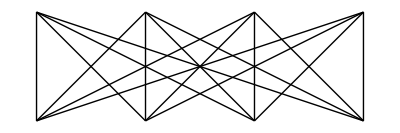

```mathematica
Graphics[Values[[AssociationOuter[Line[ {##}]&,Table[{x,1},{x,4}],Table[{x,2},{x,4}],1]]]]
```

Generate all possible binary trees with nodes from f and leaves from e to depth n:

```mathematica
trees[f_,e_,1]=e;
trees[f_,e_,n_]:=Flatten[Table[AssociationOuter[#,trees[f,e,r],trees[f,e,n-r]],{r,n-1}]&/@f]
```

```mathematica
trees[{f},{a,b},3]
```

{<|a→<|<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>→f[a,<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>]|>,b→<|<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>→f[b,<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>]|>|>,<|<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>→<|a→f[<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>,a],b→f[<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>,b]|>|>}

### Properties & Relations

If each of the list_i are duplicate-free, dimensions of the result are a concatenation of the dimensions of the inputs:

```mathematica
AssociationOuter[f,{a,b,c},{1,2,3,4}]
```

<|a→<|1→f[a,1],2→f[a,2],3→f[a,3],4→f[a,4]|>,b→<|1→f[b,1],2→f[b,2],3→f[b,3],4→f[b,4]|>,c→<|1→f[c,1],2→f[c,2],3→f[c,3],4→f[c,4]|>|>

```mathematica
Dimensions[%]
```

{3,4}

If there are duplicates, the dimensions will correspond to the number of unique elements in each list_i:

```mathematica
AssociationOuter[f,{a,a,a},{1,2,2,3}]
```

<|a→<|1→f[a,1],2→f[a,2],3→f[a,3]|>|>

```mathematica
Dimensions[%]
```

{1,3}

Compare to Outer, which is unaffected by duplicates:

```mathematica
Outer[f,{a,a,a},{1,2,2,3}]
```

{{f[a,1],f[a,2],f[a,2],f[a,3]},{f[a,1],f[a,2],f[a,2],f[a,3]},{f[a,1],f[a,2],f[a,2],f[a,3]}}

```mathematica
Dimensions[%]
```

{3,4}

Use Map and Values to convert the result into the format given by Outer:

```mathematica
AssociationOuter[f,{a,b},{x,y,z}]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

```mathematica
Map[Values,%,{0,1}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

AssociationKeyFlatten can be used to convert the result into a flat association:

```mathematica
as=AssociationOuter[f,{a,b},{x,y,z}]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

```mathematica
flat={{"[◼]", "AssociationKeyFlatten"}}[as]
```

<|{a,x}→f[a,x],{a,y}→f[a,y],{a,z}→f[a,z],{b,x}→f[b,x],{b,y}→f[b,y],{b,z}→f[b,z]|>

Restore the nested structure with AssociationKeyDeflatten:

```mathematica
{{"[◼]", "AssociationKeyDeflatten"}}[flat]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

Distributepaclet:ref/Distribute forms the same combinations of all elements, but in a flat structure:

```mathematica
Distribute[{{a,b,c},{x,y}},List]
```

{{a,x},{a,y},{b,x},{b,y},{c,x},{c,y}}

```mathematica
AssociationOuter[List,{a,b,c},{x,y}]
```

<|a→<|x→{a,x},y→{a,y}|>,b→<|x→{b,x},y→{b,y}|>,c→<|x→{c,x},y→{c,y}|>|>

Use AssociationKeyFlatten and Values to get the same result:

```mathematica
Values[{{"[◼]", "AssociationKeyFlatten"}}[%]]
```

{{a,x},{a,y},{b,x},{b,y},{c,x},{c,y}}

AssociationOuter relates to Outer much like AssociationMap relates to Map:

```mathematica
AssociationOuter[f,{1,2,3}]
```

<|1→f[1],2→f[2],3→f[3]|>

```mathematica
Outer[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
AssociationMap[f,{1,2,3}]
```

<|1→f[1],2→f[2],3→f[3]|>

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

### Possible Issues

Unlike Outer, the head must be Listpaclet:ref/List:

```mathematica
AssociationOuter[g,f[a,b],f[x,y,z]]
```

AssociationOuter::list: List expected at position 2 in AssociationOuter[g,f[a,b],f[x,y,z]].

Failure[…]

```mathematica
Outer[g,f[a,b],f[x,y,z]]
```

f[f[g[a,x],g[a,y],g[a,z]],f[g[b,x],g[b,y],g[b,z]]]

Unlike Outer, at least two arguments are required:

```mathematica
AssociationOuter[f]
```

AssociationOuter::argm: AssociationOuter called with 1 arguments; 2 or more arguments are expected.

Failure[…]

```mathematica
Outer[f]
```

f[]

Values are nested by arguments in the order they were given to f, even if f is Orderless:

```mathematica
as=AssociationOuter[Plus,{1,2,3},{4,5}]
```

<|1→<|4→5,5→6|>,2→<|4→6,5→7|>,3→<|4→7,5→8|>|>

```mathematica
as[4,1]
```

Missing[KeyAbsent,4]

```mathematica
as[1,4]
```

5